Cost of NVIDIA V100 Google Cloud per hour

```mathematica
2.28
```

2.28

training on 512 NVIDIA V100 GPU for 10 days

```mathematica
2.28 24 10 512
```

280166.

```mathematica
3.14 10^23/(7 10^12)/3600
```

1.24603×10^7

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ugo\Desktop\Daten contact\Research\KI\NLP Models

```mathematica
data=Import["NLP_Models.xlsx"][[1]];
```

```mathematica
tdata=data[[2;;-1,{1,2,4}]] ;(*First, second and fourth column, first row discarded*)
```

```mathematica
modelnames=tdata[[All,1]]
```

{Ulmfit,ELMO,BERT,GPT-2,XLNet-Large,RoBERTa,Megatron-LM,ALBERT,T5,BART,PEGASUS,GPT-3,Turing-NLG,ELECTRA,Megatron-Turing NLG,Gopher,M6-10T}

```mathematica
sizes=tdata[[All,3]];
```

```mathematica
sizetoword[n_]:=If[n<10^9,IntegerString[Round[n/10^6]]<>"M",IntegerString[Round[n/10^9]]<>"B"]
```

```mathematica
sizetoword/@sizes
```

{3M,94M,340M,2B,340M,340M,8B,235M,11B,380M,568M,175B,17B,340M,530B,280B,10000B}

```mathematica
annotations={modelnames,sizetoword/@sizes}//Transpose//Map[StringJoin[#[[1]]," ",#[[2]]]&]
```

{Ulmfit 3M,ELMO 94M,BERT 340M,GPT-2 2B,XLNet-Large 340M,RoBERTa 340M,Megatron-LM 8B,ALBERT 235M,T5 11B,BART 380M,PEGASUS 568M,GPT-3 175B,Turing-NLG 17B,ELECTRA 340M,Megatron-Turing NLG 530B,Gopher 280B,M6-10T 10000B}

```mathematica
tabledata=tdata[[All,{2,3}]];
```

```mathematica
logdata=Map[{#[[1]],#[[2]]/10^9}&,tabledata];
```

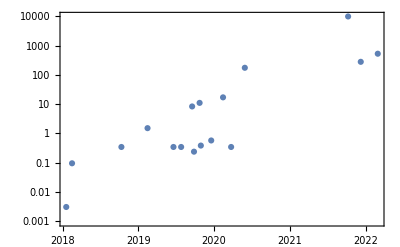

```mathematica
DateListLogPlot[logdata, PlotRange->All,PlotMarkers->Automatic,Joined->False]
```

```mathematica
labeledlogdata=Table[
	Labeled[
		logdata[[i]],Text[Style[annotations[[i]],10]]],{i,1,Length[logdata]}];
```

```mathematica
p1=DateListLogPlot[labeledlogdata, 
	PlotRange->All,
	PlotMarkers->Automatic,
	Joined->False,
	FrameLabel->{{Text[Style["Anzahl Parameter in Milliarden",Bold,12]],None},{Text[Style["Zeit",Bold,12]],None}},
	LabelStyle-> Directive[Black, 10],ImageSize->Full];
```

```mathematica
placements=Table[Automatic,Length[annotations]];
```

```mathematica
placements[[5]]=Before;placements[[6]]=Below;placements[[8]]=After;placements
```

{Automatic,Automatic,Automatic,Automatic,Before,Below,Automatic,After,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic}

```mathematica
sizefactor=1;
```

```mathematica
calloutlogdata=Table[
	Callout[
		logdata[[i]],Text[Style[annotations[[i]],14]],placements[[i]],LabelVisibility->All],{i,1,Length[logdata]}];
```

```mathematica
p2=DateListLogPlot[calloutlogdata, 
	PlotRange->All,
	PlotMarkers->Automatic,
	Joined->False,
	FrameLabel->{{Text[Style["Number of Parameters [10^9]",18]],None},{Text[Style["Time",18]],None}},
	LabelStyle-> Directive[Black, 14],
	DateTicksFormat->{"Year"},
	FrameTicks->{{{0.01,0.1,1,10,100,1000,10000},None},{Automatic,None}},
	ImageSize->Full]
```

-Graphics-

```mathematica
absdata={AbsoluteTime[#[[1]]],Log10[#[[2]]]}&/@logdata;
```

```mathematica
timedata=absdata[[All,1]];
```

```mathematica
mint=Min[absdata[[All,1]]];maxt=Max[absdata[[All,1]]];
```

```mathematica
lm=LinearModelFit[absdata,x,x]//Normal
```

-145.479+3.85661×10^-8 x

```mathematica
nsecondsyear=AbsoluteTime[{2022,1,1,0,0,0}]-AbsoluteTime[{2021,1,1,0,0,0}];
```

```mathematica
loggrowthperyear=nsecondsyear 3.85661 10^-8
```

1.21622

```mathematica
growthperyear=10^loggrowthperyear
```

16.4521

```mathematica
lmf=Function[y,lm/. x->y];
```

```mathematica
regline={DateObject/@timedata,Power[10,lmf/@ timedata]}//Transpose;
```

```mathematica
regplot=DateListLogPlot[regline,PlotStyle->Red];
```

```mathematica
completePlot=Show[p2,regplot]
```

-Graphics-

```mathematica
(*Export["nlp_models_sizes_over_time.png",completePlot,ImageSize->{1200,720}]*)
```

```mathematica
(*Export["nlp_models_sizes_over_time.svg",completePlot,ImageSize->{1200,720}]*)
```

```mathematica
(*Export["nlp_models_sizes_over_time_2400.png",completePlot,ImageSize->{2400,1440}];*)
```

```mathematica
(*Export["nlp_models_sizes_over_time_4800.svg",completePlot,ImageSize->{4800,2880}];*)
```

Scaling Loss from Kaplan, https://arxiv.org/abs/2001.08361

```mathematica
scalingLoss[n_]:=(n/(8.8 10^13))^-0.076
```

Loss reduced by 1 for 10 x larger model:

```mathematica
10^-0.076
```

0.83946

```mathematica
Table[{10^i,scalingLoss[10^i]},{i,1,10}]//TableForm
```

10 | 9.63342
100 | 8.08687
1000 | 6.78861
10000 | 5.69876
100000 | 4.78388
1000000 | 4.01588
10000000 | 3.37117
100000000 | 2.82996
1000000000 | 2.37564
10000000000 | 1.99425